## Bond-based beam model

For paper: Bond-based nonlocal models by nonlocal operator method in symmetric support domain

#### Exact solution for simply supported beam and clamped beam

```mathematica
-Graphics--Graphics-
-Graphics-(* bond-based gradient elasticity*)
-Graphics- (*bond-based thin plate*)
```

-Graphics- -Graphics-

-Graphics-

-Graphics-

```mathematica
(*cbbtp---- Coefficient of Bond-Based Thin Plate*)
```

```mathematica
cbbtp=El t^3/2/Integrate[π r r^3,{r,0,δ}]
cbbtp=El t^3/2/Integrate[π 1/r r^3,{r,0,δ}]
cbbtp=El t^3/2/Integrate[π 1 r ^3,{r,0,δ}]
```

(25 G t^3)/(4 π δ^5)

(15 G t^3)/(4 π δ^3)

(5 G t^3)/(π δ^4)

```mathematica
(*cbbge---- Coefficient of Bond-Based Gradient elasticity*)
```

```mathematica
cbbge=15 ll^2 2/5 El/Integrate[π r^4 1,{r,0,δ}]
cbbge=15 ll^2 2/5 El/Integrate[π r^4 r,{r,0,δ}]
cbbge=15 ll^2 2/5 El/Integrate[π r^4 1/r,{r,0,δ}]
```

(75 G ll^2)/(π δ^5)

(90 G ll^2)/(π δ^6)

(60 G ll^2)/(π δ^4)

```mathematica
(*x0=10^-3;Plot[Sign[x] Min[ Abs[x],  x0^2/Abs[x]],{x,-30x0,30x0},PlotRange->All]*)
```

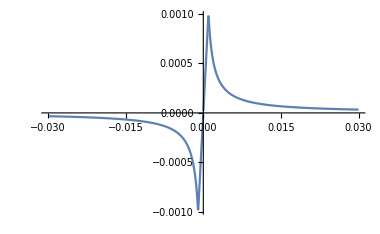
```mathematica
(*-Graphics-*)(*Using this model can be used for force softening.*)
```

```mathematica
(*Compiled function for internal force calculation. nexp--exponent of weight function. w(r)=r^nexp*)
InternalForceThinBeam2=Compile[{{wList,_Real,1},{coord0,_Real,1},{nei,_Integer},{cbt,_Real},{dx,_Real},{nexp,_Real},{kappaDam,_Real}},Block[{f,wij=0.,fij=0.,rij=0.,nn=Length[coord0],dstate,κ0,dx2=dx^2},f=Table[0.,{nn}];dstate=Table[0.,{nn}];Do[Do[wij=wList[[j+i]]+wList[[i-j]]-2wList[[i]];
rij=Abs[coord0[[j+i]]-coord0[[i]]];
κ0=wij/rij^2;
If[i>3nei&& i<nn-3nei&& Abs[κ0]>kappaDam,dstate[[i]]+=1;κ0=kappaDam^2/κ0];
fij=cbt κ0 rij^(nexp-2)(dx2);
f[[i]]+=2fij;f[[j+i]]-=fij;f[[i-j]]-=fij;,{j,1,nei}];,{i,nei+1,nn-nei}];{f,dstate}]];
(*BBPDc1a get the coefficient of c*)
BBPDc1a[El_,h_,delta_,nexp_:1]:=Block[{r},Print["Weight function:w[r]:="<>ToString[InputForm[r^nexp]]];Switch[nexp,0,(El h^3)/(12 delta),1,El h^3/(6 delta^2),2, El h^3/(12 1/3 delta^3),3 ,El h^3/(12 1/4 delta^4)]];
ClearAll[SaveToCell];
SaveToCell::usage="SaveToCell[variable] creates an input cell that reassigns the current value of variable.\n"<>"SaveToCell[variables, display] shows 'display' on the right-hand-side of the assignment.";
SetAttributes[SaveToCell,HoldFirst]
SaveToCell[var_,name:Except[_?OptionQ]:"data",opt:OptionsPattern[]]:=With[{data=Compress[var],panel=ToBoxes@Tooltip[Panel[name,FrameMargins->Small],DateString[]]},CellPrint@Cell[BoxData@RowBox[{MakeBoxes[var],"=",InterpretationBox[panel,Uncompress[data]],";"}],"Input",(*prevent deletion by Cell>Delete All Output:*)GeneratedCell->False,(*CellLabel is special:last occrrence takes precedence,so it comes before opt:*)CellLabel->"(saved)",opt,CellLabelAutoDelete->False]];
```

#### Simulation of simply supported beam

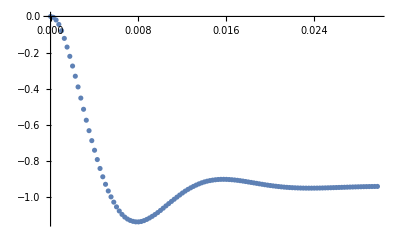
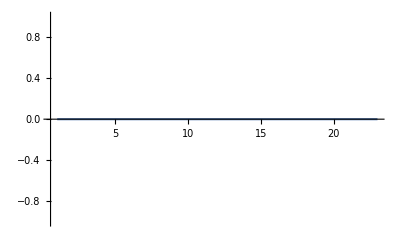
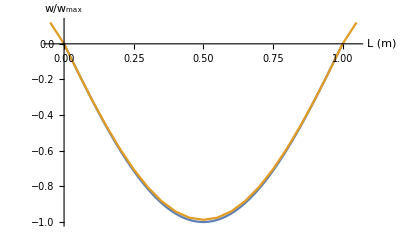

```mathematica
El=30*10^9;L=1;h=0.05;ih=h^3/12;dx=0.05;nx=2;Nx=Round[L/dx];
L=1;δfun=-q x(L^3-2 L x^2+x^3)/(24  El ih);
wmaxSimple=δfun/.{q->10^3,x->L/2};
(*exact solution for simply supported beam under uniform pressure*)
wfs=Table[{x,δfun/.{q->10^3}},{x,0,L,L/100.}];
wMax=Abs[δfun/.{q->10^3,x->L/2}];
wfs[[All,2]]/=wMax;
nexp=0;tMax=0.03;
delta=nx dx+0. dx; cbb=BBPDc1a[El,h,delta,nexp];
Print["Simulation of simply supported beam\n support radius δ:",delta/dx,", number of nodes No.:",Nx]
xlist=Range[-nx+1,Nx+nx-1]dx;
wlist=0. xlist;simpleSupport=True;
acc=wlist;
accNew=acc;pen=  400;(*penalty for damping*)
velo=wlist;
qa=-1 10^3 dx;
externalForce=acc;
externalForce+=qa;
rho=3000;
mi=h dx rho;
flist=0 xlist;

outputInterval=2;
j=1;
tInc=2 10.^-6dx/0.02;
nstep=Round[tMax/tInc];
Print[ "Number of steps:",nstep]
pmass=mi;Ul={};Vl={};Al={};dstateA={};ctime=0.;
Monitor[Do[wlist+=tInc velo+(0.5 tInc^2)acc;
If[simpleSupport,(*the deflection is antisymmetric for simply supported beam.*)wlist[[nx]]=0.;wlist[[-nx]]=0.;,
wlist[[1;;(nx)]]=0.;wlist[[-(nx);;-1]]=0.;];
AppendTo[Ul,wlist];
{internalF,dstate}= InternalForceThinBeam2[wlist,xlist,nx,cbb,dx,nexp, 10^5 0.0004(*very large value so that no damage will happen*)];
accNew=(internalF+externalForce-pen velo pmass)/pmass;
AppendTo[Al,accNew];
AppendTo[dstateA,-dstate];
velo+=0.5 tInc (acc+accNew);
AppendTo[Vl,velo];
acc=accNew;
ctime+=tInc;j++;,{i,nstep}],j];
Print["Maximal relative deflection :",Min[Ul[[-1]]/wMax]]
{ListPlot[{Range[Length[Ul]]tInc,Ul[[All,Round[Nx/2]]]/wMax}ᵀ[[1;;-1;;50]]],ListPlot[dstateA[[-1]],PlotRange->All,Joined->True],ListPlot[{wfs,{xlist,Ul[[-1]]/wMax}ᵀ},PlotRange->All,Joined->True,AxesLabel->{"L (m)","w/w_max"}]}
```

#### Simply supported beam with damage.

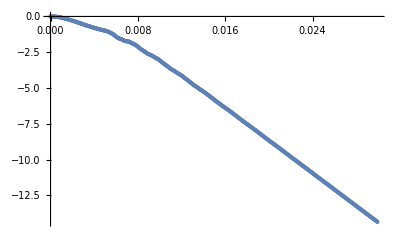
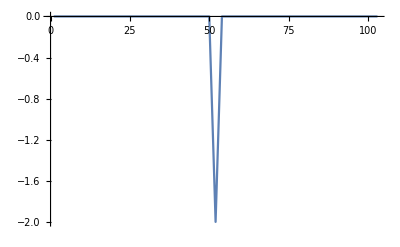
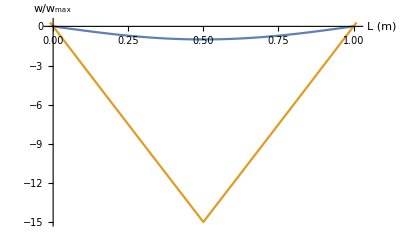

```mathematica
El=30*10^9;L=1;h=0.05;ih=h^3/12;dx=0.01;nx=2;Nx=Round[L/dx];
L=1;δfun=-q x(L^3-2 L x^2+x^3)/(24  El ih);
wmaxSimple=δfun/.{q->10^3,x->L/2};
(*exact solution for simply supported beam under uniform pressure*)
wfs=Table[{x,δfun/.{q->10^3}},{x,0,L,L/100.}];
wMax=Abs[δfun/.{q->10^3,x->L/2}];
wfs[[All,2]]/=wMax;
nexp=0;tMax=0.03;
delta=nx dx+0. dx; cbb=BBPDc1a[El,h,delta,nexp];
Print["Simulation of simply supported beam\n support radius δ:",delta/dx,", number of nodes No.:",Nx]
xlist=Range[-nx+1,Nx+nx-1]dx;
wlist=0. xlist;simpleSupport=True;
acc=wlist;
accNew=acc;pen=  400;(*penalty for damping*)
velo=wlist;
qa=-1 10^3 dx;
externalForce=acc;
externalForce+=qa;
rho=3000;
mi=h dx rho;
flist=0 xlist;

outputInterval=2;
j=1;
tInc=2 10.^-6dx/0.02;
nstep=Round[tMax/tInc];
Print[ "Number of steps:",nstep]
pmass=mi;Ul={};Vl={};Al={};dstateA={};ctime=0.;
Monitor[Do[wlist+=tInc velo+(0.5 tInc^2)acc;
If[simpleSupport,(*the deflection is antisymmetric for simply supported beam.*)wlist[[nx]]=0.;wlist[[-nx]]=0.;,
wlist[[1;;(nx)]]=0.;wlist[[-(nx);;-1]]=0.;];
AppendTo[Ul,wlist];
{internalF,dstate}= InternalForceThinBeam2[wlist,xlist,nx,cbb,dx,nexp,  0.0004(*very large value so that no damage will happen*)];
accNew=(internalF+externalForce-pen velo pmass)/pmass;
AppendTo[Al,accNew];
AppendTo[dstateA,-dstate];
velo+=0.5 tInc (acc+accNew);
AppendTo[Vl,velo];
acc=accNew;
ctime+=tInc;j++;,{i,nstep}],j];
Print["Maximal relative deflection :",Min[Ul[[-1]]/wMax]]
{ListPlot[{Range[Length[Ul]]tInc,Ul[[All,Round[Nx/2]]]/wMax}ᵀ[[1;;-1;;50]]],ListPlot[dstateA[[-1]],PlotRange->All,Joined->True],ListPlot[{wfs,{xlist,Ul[[-1]]/wMax}ᵀ},PlotRange->All,Joined->True,AxesLabel->{"L (m)","w/w_max"}]}
```